```mathematica
SetDirectory["/Users/mobileryan/Triplet-ESR"]
```

/Users/mobileryan/Triplet-ESR

```mathematica
SetDirectory["/home/goluckyryan/Desktop/nonLinearFit"]
```

/home/goluckyryan/Desktop/nonLinearFit

```mathematica
Directory[]
```

/home/goluckyryan/Dropbox/ExperimentDoc/Triplet-DNP/Analysis_Programs/old

```mathematica
SetDirectory["C:\\Users\\goluc\\Desktop\\nonLinearFit"]
```

C:\Users\goluc\Desktop\nonLinearFit

```mathematica
preData=Import["./test.dat","CSV" ];
{dimT, dump}=Dimensions[preData[[2;;-1]]]
BData=Drop[Drop[preData[[1]],1],-1];
dimB=Length[BData]
DataB[B_]:=Table[{preData[[i,1]],preData[[i,B+1]]},{i,2,dimT}]
DataT[t_]:=Table[{preData[[1,i]],preData[[t+1,i+1]]},{i,1,dimB}]
```

{1002,352}

350

```mathematica
tempData=Transpose[preData[[2;;-1, 2;;-3]]];
Dimensions[tempData]
ArrayPlot[tempData,ColorFunction->"Rainbow",AspectRatio->1]
{Max[tempData], Min[tempData]}
```

{349,1002}

-Graphics-

{41.34,-34.17}

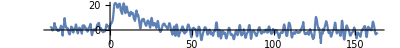

{B-Field,3.213,2.4,mean,1.03766,sd,2.23107}

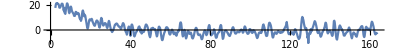

```mathematica
id=104;
fitStartT=195;
dataB=DataB[id];
ListPlot[dataB, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full] 
{"B-Field",BData[[id]],dataB[[fitStartT,1]],"mean",noiseLevel=Mean[dataB[[1;;fitStartT-20,2]]], "sd",sd=StandardDeviation[dataB[[1;;fitStartT-20,2]]]}
g1=ListPlot[dataB[[fitStartT;;-1]], Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
```

```mathematica
Func[t_,a_,Ta_]:=a Exp[-t/Ta]
f[t_,par_]:=Func[t,par[[1]],par[[2]]]+Func[t,par[[3]],par[[4]]]
F[t_,par_]:={ⅇ^(-t/par[[2]]),(par[[1]] ⅇ^(-t/par[[2]]) t)/par[[2]]^2,ⅇ^(-t/par[[4]]),(par[[3]] ⅇ^(-t/par[[4]]) t)/par[[4]]^2}
```

FittedModel::constr: The property values {ANOVATable,ParameterConfidenceIntervalTable,ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 25.7586 | 5.96046×10^10 | 4.32157×10^-10 | 1
Ta | 13.5131 | 8.7558×10^6 | 1.54333×10^-6 | 0.999999
b | 3.15239 | 5.96046×10^10 | 5.28884×10^-11 | 1
Tb | 13.5206 | 7.15579×10^7 | 1.88947×10^-7 | 1, | DF | SS | MS
Model | 4 | 20090.9 | 5022.74
Error | 803 | 8254.31 | 10.2793
Uncorrected Total | 807 | 28345.3 | 
Corrected Total | 806 | 27283.6 | , | Estimate | Standard Error | Confidence Interval
a | 25.7586 | 5.96046×10^10 | {-1.16999×10^11,1.16999×10^11}
Ta | 13.5131 | 8.7558×10^6 | {-1.71869×10^7,1.7187×10^7}
b | 3.15239 | 5.96046×10^10 | {-1.16999×10^11,1.16999×10^11}
Tb | 13.5206 | 7.15579×10^7 | {-1.40463×10^8,1.40463×10^8}}

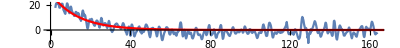

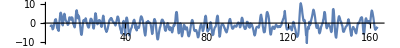

{mean,-0.878744,sd,3.07159,1.37673}

```mathematica
nlm=NonlinearModelFit[dataB[[fitStartT;;-1]],{f[t,{a,Ta,b,Tb}], 0<Ta <Tb}, {a, Ta, b, Tb}, t,AccuracyGoal->1, PrecisionGoal->1];
nlm[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
Show[
g1,
Plot[nlm[t],{t,0,200}, PlotRange->All, PlotStyle->Red]
]
diff=Table[{dataB[[i,1]],dataB[[i,2]]-nlm[dataB[[i,1]]]},{i,200,Length[dataB]}];
ListPlot[diff, Joined->True, AspectRatio->1/10,PlotRange->All, ImageSize->Full]
{"mean",Mean[diff[[1;;-1,2]]], "sd",fitSigma=StandardDeviation[diff[[1;;-1,2]]], fitSigma/sd}
```

## Manual Method

```mathematica
X=dataB[[fitStartT;;-1]][[1;;-1,1]];
Y=dataB[[fitStartT;;-1]][[1;;-1,2]];
n=Length[X];
SSRcoun= Table[{b, Tb, 
fn =Table[f[X[[i]], {55, 28, b, Tb}],{i,Length[X]}];
SSRn=(Y - fn).(Y-fn)/n},{b,-40,-20, 2}, {Tb, 20, 80,2}];
{mi,mj}=Dimensions[SSRcoun][[{1,2}]];
Min[Table[SSRcoun[[i,j,3]],{i,1,mi},{j,1,mj}]]
%*n
```

8.80606

7106.49

```mathematica
12 n
```

9684

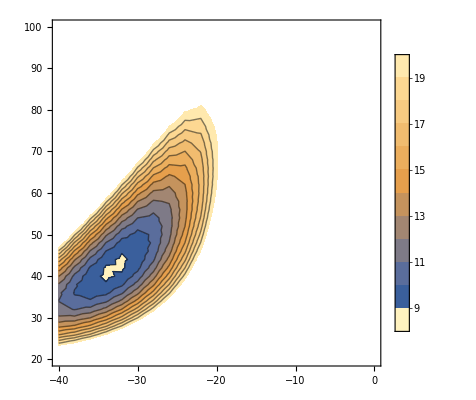

```mathematica
ListContourPlot[Flatten[SSRcoun,1],
PlotRange->{0,20},
Contours->Table[i,{i,7,20,1}],
InterpolationOrder->3,PlotLegends->Automatic]
```

```mathematica
DF=803;α=0.95;
tStat=Table[temp[[1,i]]/temp[[2,i]],{i,1,4}]
pValue=Table[2(1-CDF[StudentTDistribution[DF],Abs[tStat[[i]]]]),{i,1,4}]
CF=Table[
temp[[1,i]]+
temp[[2,i]]{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]},{i,1,4}]
```

{1.74526,4.84665,-0.678331,2.36191}

{0.0813214,1.50736×10^-6,0.497757,0.018419}

{{-8.03612,136.909},{17.9915,42.4848},{-98.8684,48.0853},{9.37862,101.661}}

```mathematica
newPar2[par_,dataB_]:=Module[
{fa,Fa, Y,X, par1,CoVar, error, var, DF, GMat},
X=dataB[[1;;-1,1]];
Y=dataB[[1;;-1,2]];
fa=Table[Func[X[[i]], par[[1]],par[[2]]],{i,Length[X]}];
Fa=Table[F2[X[[i]], par],{i,Length[X]}];
GMat=Inverse[Transpose[Fa].Fa].Transpose[Fa];
par1=par+GMat.(Y-fa);
DF=Length[X]-Length[par];
var=(Y-fa).(Y-fa)/DF;
CoVar=var Inverse[Transpose[Fa].Fa];
error=Table[√CoVar[[i,i]],{i,1,Length[par]}];
{par1,error, var,DF}
]
```

```mathematica
temp2=newPar2[{50,30},dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
temp2=newPar2[temp2[[1]],dataB[[fitStartT;;-1]]]
```

{{42.0385,18.115},{1.32321,1.03401},47.0199,805}

{{43.21,18.0827},{0.909289,0.483381},10.8097,805}

{{43.1979,18.0916},{0.908267,0.468798},10.7557,805}

{{43.2012,18.0894},{0.907925,0.469012},10.7557,805}

{{43.2004,18.0899},{0.908009,0.468955},10.7557,805}

{{43.2006,18.0898},{0.907988,0.468969},10.7557,805}

{{43.2005,18.0898},{0.907994,0.468966},10.7557,805}

{{43.2005,18.0898},{0.907992,0.468966},10.7557,805}

```mathematica
nlm2[{"ParameterTable","ANOVATable","ParameterConfidenceIntervalTable"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 43.2005 | 0.907993 | 47.5781 | 3.98102×10^-236
Ta | 18.0898 | 0.468966 | 38.5738 | 3.69199×10^-185, | DF | SS | MS
Model | 2 | 64018.5 | 32009.3
Error | 805 | 8658.36 | 10.7557
Uncorrected Total | 807 | 72676.9 | 
Corrected Total | 806 | 64550.3 | , | Estimate | Standard Error | Confidence Interval
a | 43.2005 | 0.907993 | {41.4182,44.9828}
Ta | 18.0898 | 0.468966 | {17.1693,19.0104}}

```mathematica
DF2=805;α=0.95;
tStat2=Table[temp2[[1,i]]/temp2[[2,i]],{i,1,2}]
pValue2=Table[2(1-CDF[StudentTDistribution[DF2],Abs[tStat2[[i]]]]),{i,1,2}]
CF2=Table[
temp2[[1,i]]+
temp2[[2,i]]{InverseCDF[StudentTDistribution[DF2],(1-α)/2],InverseCDF[StudentTDistribution[DF2],(1+α)/2]},{i,1,2}]
```

{47.5777,38.5742}

{0.,0.}

{{41.4182,44.9828},{17.1693,19.0104}}

## Fourier Analysis

```mathematica
SwapData[fdata_]:=Module[{n,m},n=Length[fdata];If[Mod[n,2]==1,m=(n+1)/2,m=n/2];Join[fdata⟦m+1;;-1⟧,fdata⟦1;;m⟧]]
SwapDataBack[fdata_]:=Module[{n,m},n=Length[fdata];If[Mod[n,2]==1,m=(n+1)/2,m=n/2];Join[fdata⟦m;;-1⟧,fdata⟦1;;m-1⟧]]
DiscreteFourier[data_,id_]:=Module[{n,m,dω,fdata},
n=Length[data];If[Mod[n,2]==1,m=(n+1)/2,m=n/2];dω=1/(data⟦-1,1⟧-data⟦1,1⟧);fdata=Fourier[data⟦1;;-1,2⟧];fdata=If[id==0,Re[fdata],Im[fdata]];fdata=SwapData[fdata];Table[{dω (i-m),fdata⟦i⟧},{i,1,n}]]
InverseDiscreteFourier[data_,dataC_,dataS_]:=Module[{n,m,dω,gdata,fdata},
n=Length[dataC];If[Mod[n,2]==1,m=(n+1)/2,m=n/2];dω=1/(dataC⟦-1,1⟧-dataC⟦1,1⟧);gdata=Table[dataC⟦i,2⟧+ⅈ dataS⟦i,2⟧,{i,1,n}];gdata=SwapDataBack[gdata];fdata=InverseFourier[gdata];Table[{data[[i,1]],Re[fdata⟦i⟧]},{i,1,n}]]
```

```mathematica
GatedFourierAnalysis[data_,gate_, plotFlag_]:=Module[{n,m,ffc,ffs,ggc,ggs, ω},
ffc=DiscreteFourier[data,0];
ffs=DiscreteFourier[data,1];
n=Length[data];
m=(n+1)/2;
ω=DeleteCases[Table[If[Abs[i-m]≤ gate,ffc[[i,1]],{ 0}],{i,1,n}],{0}];
ggc=Table[{ffc[[i,1]],If[Abs[i-m]≤ gate,ffc[[i,2]], 0]},{i,1,n}];
ggs=Table[{ffs[[i,1]],If[Abs[i-m]≤ gate,ffs[[i,2]], 0]},{i,1,n}];
If[plotFlag==1,Print["max",Max[ω], "; min",Min[ω]];Print[ListPlot[{ffc,ffs, ggc,ggs},Joined->True, AspectRatio->0.2,ImageSize->Full, PlotRange->{{-0.5,0.5},All}]]];
InverseDiscreteFourier[data,ggc,ggs]
]
```

max0.1; min-0.1

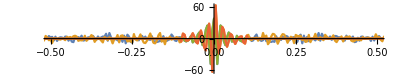

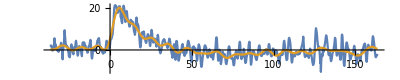

```mathematica
tt=DataB[id];
gg=GatedFourierAnalysis[tt,20,1];
ListPlot[{tt,gg},Joined->True, PlotRange->All, AspectRatio->0.2,ImageSize->Full]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{ | Estimate | Standard Error | t-Statistic | P-Value
a | 18.2573 | 8.64673×10^10 | 2.11146×10^-10 | 1
Ta | 14.0637 | 1.32727×10^7 | 1.0596×10^-6 | 0.999999
b | 9.13013 | 8.64673×10^10 | 1.05591×10^-10 | 1
Tb | 14.0693 | 2.65446×10^7 | 5.30027×10^-7 | 1.},{ | Estimate | Standard Error | t-Statistic | P-Value
a | 25.7586 | 5.96046×10^10 | 4.32157×10^-10 | 1
Ta | 13.5131 | 8.7558×10^6 | 1.54333×10^-6 | 0.999999
b | 3.15239 | 5.96046×10^10 | 5.28884×10^-11 | 1
Tb | 13.5206 | 7.15579×10^7 | 1.88947×10^-7 | 1}}

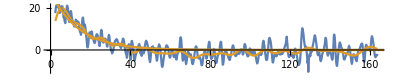

```mathematica
nlm2=NonlinearModelFit[gg[[fitStartT;;-1]],{f[t,{a,Ta,b,Tb}], 0<Ta <Tb}, {a, Ta, b, Tb}, t,AccuracyGoal->1, PrecisionGoal->1];
{nlm2[{"ParameterTable"}],nlm[{"ParameterTable"}]}
Show[
ListPlot[{
tt[[fitStartT;;-1]],
gg[[fitStartT;;-1]]
},Joined->True,PlotRange->All,AspectRatio->0.2,ImageSize->Full],
Plot[{nlm[t],nlm2[t]},{t,0,200}, PlotRange->All]
]
```

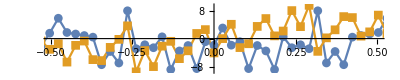

```mathematica
ffc=DiscreteFourier[tt,0];
ffs=DiscreteFourier[tt,1];
ctt=tt[[1;;190]];
cffc=DiscreteFourier[ctt,0];
cffs=DiscreteFourier[ctt,1];
ListPlot[{cffc,cffs},Joined->True, Joined->True, AspectRatio->0.2,ImageSize->Full, PlotRange->{{-0.5,0.5},All},PlotMarkers->Automatic]
```

## 2 D Fourier Analysis

```mathematica
gtempData=Monitor[Table[GatedFourierAnalysis[DataB[i],20,0][[1;;-1,2]],{i,1,350}],i];
```

```mathematica
ArrayPlot[tempData,ColorFunction->"Rainbow",AspectRatio->1]
ArrayPlot[gtempData,ColorFunction->"Rainbow",AspectRatio->1]
```

-Graphics-

-Graphics-

```mathematica
kk=Fourier[tempData];
```

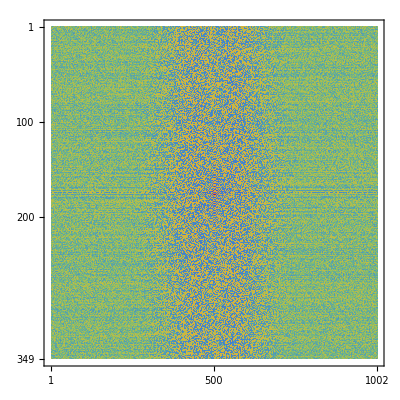

```mathematica
kk2=SwapData[Table[SwapData[kk[[i]]],{i,1,Length[kk]}]];
MatrixPlot[Re[kk2],ColorFunction->"Rainbow",AspectRatio->1, PlotRange->{All,All,All}]
```

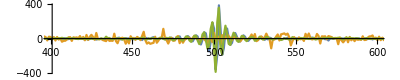

```mathematica
ListPlot[Im[kk2[[174;;176]]], Joined->True,PlotRange->{{400,600},All}, AspectRatio->0.2,ImageSize->Full]
```

```mathematica
Table[kk[[j,i]]=0,{j,{1}},{i,1,1002}];
hh=Re[InverseFourier[kk]];
ArrayPlot[hh-tempData,ColorFunction->"Rainbow",AspectRatio->1]
ArrayPlot[hh,ColorFunction->"Rainbow",AspectRatio->1]
ArrayPlot[tempData,ColorFunction->"Rainbow",AspectRatio->1]
```

-Graphics-

-Graphics-

-Graphics-

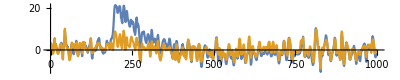

```mathematica
ListPlot[{tempData[[id]],hh[[id]]},Joined->True, PlotRange->All,PlotRange->All,AspectRatio->0.2,ImageSize->Full]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{ | Estimate | Standard Error | t-Statistic | P-Value
a | 945.038 | 807562. | 0.00117024 | 0.999067
Ta | 33.606 | 292.364 | 0.114945 | 0.908517
b | -921.497 | 807562. | -0.00114108 | 0.99909
Tb | 34.294 | 303.162 | 0.113121 | 0.909963},{ | Estimate | Standard Error | t-Statistic | P-Value
a | 25.7586 | 5.96046×10^10 | 4.32157×10^-10 | 1
Ta | 13.5131 | 8.7558×10^6 | 1.54333×10^-6 | 0.999999
b | 3.15239 | 5.96046×10^10 | 5.28884×10^-11 | 1
Tb | 13.5206 | 7.15579×10^7 | 1.88947×10^-7 | 1}}

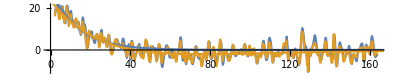

```mathematica
fithh=Table[{preData[[i,1]],hh[[id,i]]},{i,1,Length[hh[[id]]]}];
nlm3=NonlinearModelFit[fithh[[fitStartT;;-1]],{f[t,{a,Ta,b,Tb}], 0<Ta <Tb}, {a, Ta, b, Tb}, t,AccuracyGoal->1, PrecisionGoal->1];
{nlm3[{"ParameterTable"}],nlm[{"ParameterTable"}]}
Show[
ListPlot[{
tt[[fitStartT;;-1]],
fithh[[fitStartT;;-1]]
},Joined->True,PlotRange->All,AspectRatio->0.2,ImageSize->Full],
Plot[{nlm[t],nlm3[t]},{t,0,200}, PlotRange->All]
]
```